```mathematica
duffEq=(x''[t])^2+g x'[t]+x[t] (1-a x[t]^2)==f Cos[ω t];
duff[vals_,ic_,tmax_] :=Module[{nds},
nds = NDSolve[Join[{duffEq/.vals},ic],x,{t,0,tmax},MaxSteps->10000]⟦1⟧;
Print[duffEq/.vals];
Print[ParametricPlot[Evaluate[{x[t],x'[t]}/.nds],{t,0,10},AspectRatio->Automatic]];
Print[Plot[Evaluate[x[t]/.nds],{t,0,tmax}]];
]
```

x[t]+x''[t]^2==0

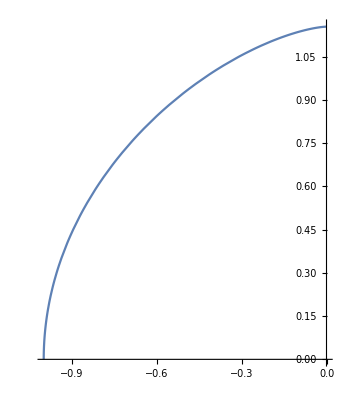

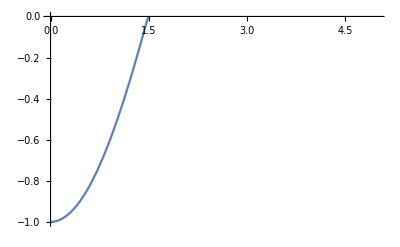

```mathematica
(*a*)
duff[{g->0,f->0,a->0,ω->.25},{x[0]==-1, x'[0]==0}, 5]
```

x[t] (1-x[t]^2)+x''[t]^2==0

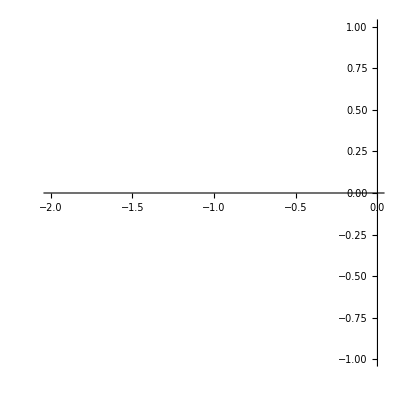

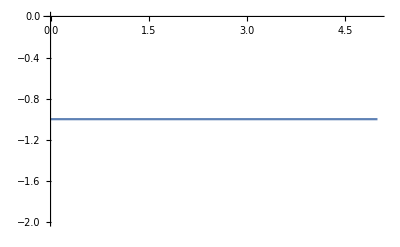

x[t] (1-x[t]^2)+x''[t]^2==0

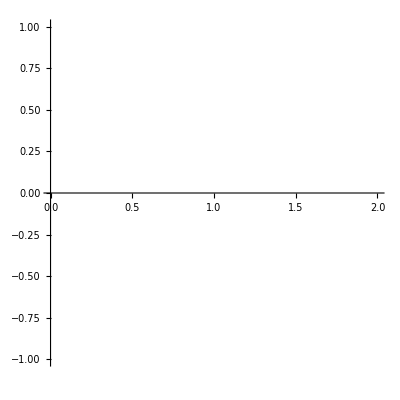

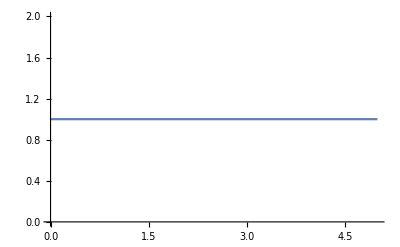

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.000273561.

x[t] (1+x[t]^2)+x''[t]^2==0

-Graphics-

-Graphics-

NDSolve::ndsz: At t == 4.84156, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.3087.

x[t] (1+x[t]^2)+x''[t]^2==0

-Graphics-

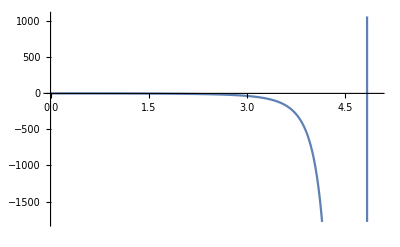

```mathematica
(*b*)
duff[{g->0,f->0,a->1,ω->.25},{x[0]==-1, x'[0]==0}, 5]
duff[{g->0,f->0,a->1,ω->.25},{x[0]==1, x'[0]==0}, 5]
duff[{g->0,f->0,a->-1,ω->.25},{x[0]==1, x'[0]==0}, 5] 
duff[{g->0,f->0,a->-1,ω->.25},{x[0]==-1, x'[0]==0}, 5] (*last doesn't go well*)
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.48754.

x[t]+0.01 x'[t]+x''[t]^2==0

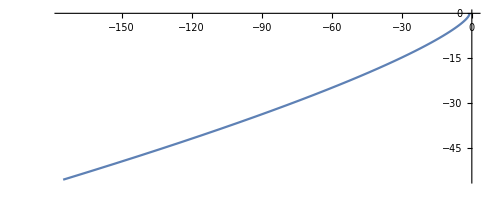

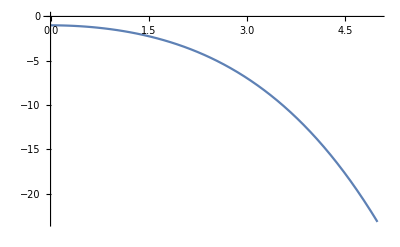

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.26817.

x[t]+0.351 x'[t]+x''[t]^2==0

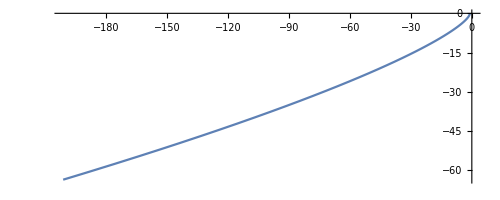

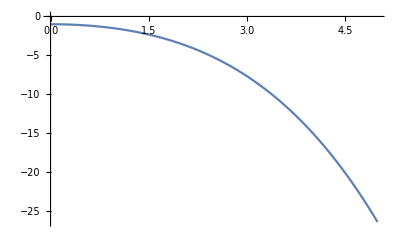

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.26817.

x[t]+0.351 x'[t]+x''[t]^2==0

-Graphics-

-Graphics-

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.54495.

x[t] (1-0.578 x[t]^2)+0.351 x'[t]+x''[t]^2==0

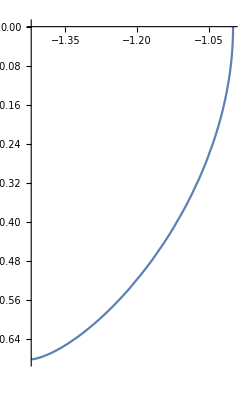

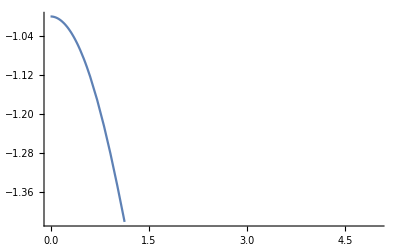

```mathematica
(*c*)
Manipulate[duff[{g->gamma,f->0,a->alpha,ω->omega},{x[0]==-1, x'[0]==0}, 5],
{gamma, .01, 1},{omega, .25, 2}, {alpha, 0, 1}]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.63474.

x[t]+x''[t]^2==Cos[0.5 t]

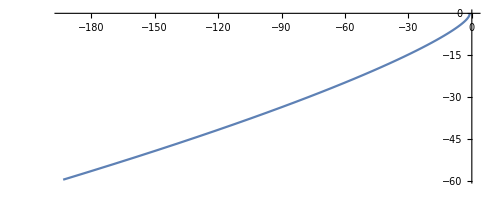

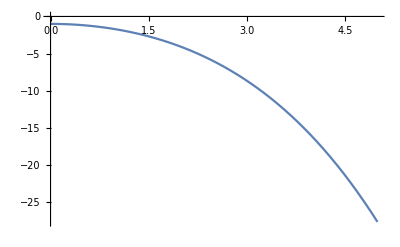

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.37866.

x[t]+x''[t]^2==Cos[1. t]

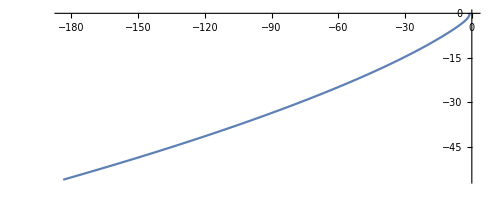

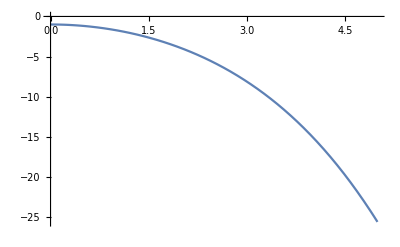

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.1585.

x[t]+x''[t]^2==Cos[1.5 t]

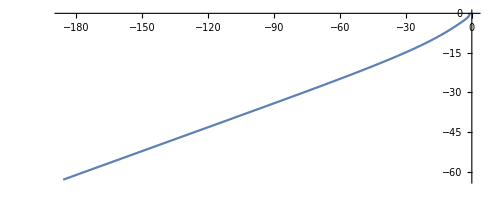

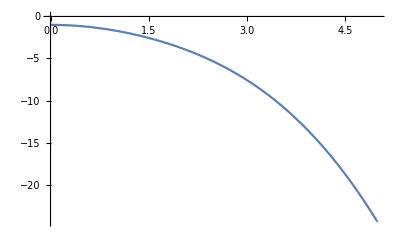

```mathematica
(*d*)
Manipulate[duff[{g->0,f->1,a->0,ω->om},{x[0]==-1, x'[0]==0}, 5],
{om, .5, 1.5,.5}]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.249294.

x[t]+x''[t]^2==Cos[π t]

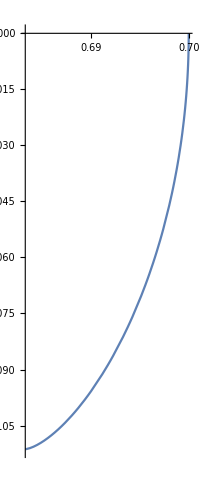

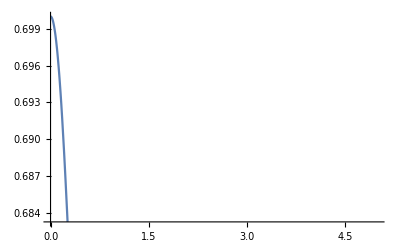

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.602061.

x[t]+x''[t]^2==Cos[π t]

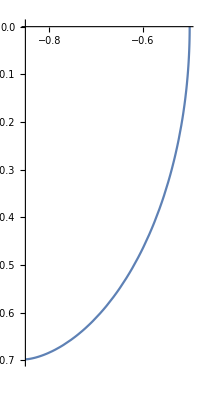

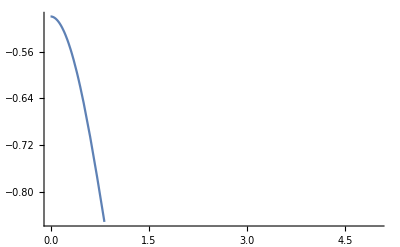

```mathematica
(*e*)
duff[{g->0,a->0,f->1,ω->Pi},{x[0]==.7, x'[0]==0}, 5]
duff[{g->0,a->0,f->1,ω->Pi},{x[0]==-.5, x'[0]==0}, 5]
```

NDSolve::ndsz: At t == 4.73686, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.46705.

x[t] (1+x[t]^2)+x''[t]^2==Cos[0.5 t]

-Graphics-

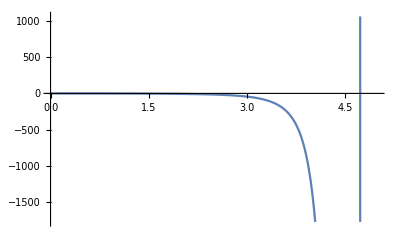

NDSolve::ndsz: At t == 4.74647, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.30945.

x[t] (1+x[t]^2)+x''[t]^2==Cos[1. t]

-Graphics-

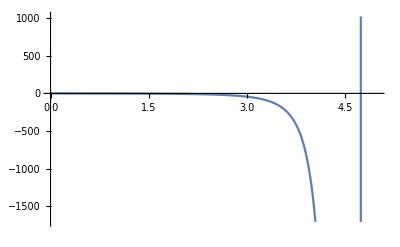

NDSolve::ndsz: At t == 4.76044, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.11193.

x[t] (1+x[t]^2)+x''[t]^2==Cos[1.5 t]

-Graphics-

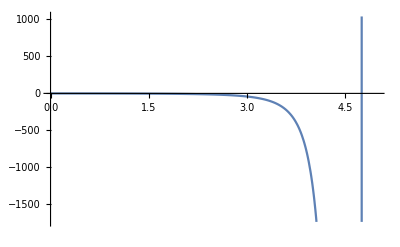

```mathematica
(*f*)
Manipulate[duff[{g->0,f->1,a->-1,ω->om},{x[0]==-1, x'[0]==0}, 5],
{om, .5, 1.5,.5}]
```

NDSolve::ndsz: At t == 4.34822, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.31908.

x[t] (1+x[t]^2)+0.1 x'[t]+x''[t]^2==10 Cos[0.5 t]

-Graphics-

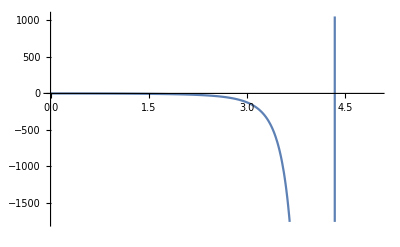

NDSolve::ndsz: At t == 4.3748, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.20697.

x[t] (1+x[t]^2)+0.1 x'[t]+x''[t]^2==10 Cos[1. t]

-Graphics-

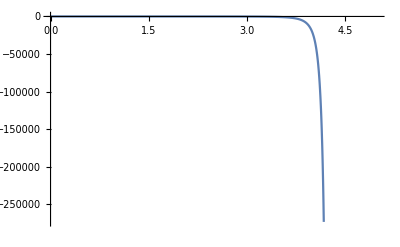

NDSolve::ndsz: At t == 4.41848, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.99033.

x[t] (1+x[t]^2)+0.1 x'[t]+x''[t]^2==10 Cos[1.5 t]

-Graphics-

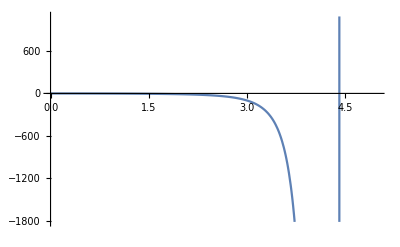

NDSolve::ndsz: At t == 4.3748, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.20697.

x[t] (1+x[t]^2)+0.1 x'[t]+x''[t]^2==10 Cos[1. t]

-Graphics-

-Graphics-

NDSolve::ndsz: At t == 4.34822, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.31908.

x[t] (1+x[t]^2)+0.1 x'[t]+x''[t]^2==10 Cos[0.5 t]

-Graphics-

-Graphics-

```mathematica
Manipulate[duff[{g->0.1,f->10,a->-1,ω->om},{x[0]==-1, x'[0]==0}, 5],
{om, .5, 1.5,.5}]
```